```mathematica
files=FileNames["*.csv",NotebookDirectory[]]
```

{/Users/yaroslav/Desktop/dataset.csv,/Users/yaroslav/Desktop/datasethi.csv,/Users/yaroslav/Desktop/hi.csv,/Users/yaroslav/Desktop/Untitled.csv}

```mathematica
importfile = files⟦1⟧
```

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
raw={{"a","n"},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}
```

{{a,n},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}

```mathematica
dataset=makeDataset[raw]
```

```mathematica
dataset1=dataset[All,<|"a"->(1/Around[#n,1]&),"b"->(1-Cos[ π Around[#a,1] /180]&)|>]
```

```mathematica
MantErr[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;2⟧],10]/10]
MantExp[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,MantissaExponent[a["Uncertainty"]]⟦2⟧-2,MantissaExponent[a["Uncertainty"]]⟦2⟧-1]
DigVal[a_]:=MantissaExponent[a["Value"]]⟦2⟧-MantExp[a]+1
MantVal[a_]:=Round[FromDigits[RealDigits[a["Value"]]⟦1,;;DigVal[a]⟧],10]/10
hiTeXForm[x_]:=Which[Head[x]===Real,IntegerPart[x],-3≤MantExp[x]≤-1,ToString[Row[{PaddedForm[MantVal[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}],"(",MantErr[x],")"}]],MantExp[x]==0,ToString[Row[{MantVal[x],"(",MantErr[x],")"}]],True,ToString[Row[{MantVal[x],"(",MantErr[x],")e",MantExp[x]}]]]
hiTeXFormVal[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[x["Value"],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantVal[x]]
hiTeXFormErr[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[MantErr[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantErr[x]]
```

```mathematica
dataset3=dataset1[All,<|"aexp"->(hiTeXForm[#a]&),"bexp"->(hiTeXForm[#b]&)|>]
```

```mathematica
dataset4=dataset1[All,<|"TexpAbs"->(hiTeXFormVal[#T]&),"TexpErr"->(hiTeXFormErr[#T]&),"WexpAbs"->(hiTeXFormVal[#W]&),"WexpErr"->(hiTeXFormErr[#W]&)|>]
```

```mathematica
Export[NotebookDirectory[]<>"datasethi.csv",dataset3,"TextDelimiters"->""]
```

/Users/yaroslav/Desktop/datasethi.csv

```mathematica
raw={Table[n+RandomInteger[],{n,10}],Table[n,{n,10}]}
```

{{2,2,3,4,6,7,7,8,9,11},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
data=Table[{dataset2[n,"LnT"]["Value"],dataset2[n,"LnW"]["Value"]},{n,11}];
dataerr=Table[{dataset2[n,"LnT"],dataset2[n,"LnW"]},{n,11}];
fit=LinearModelFit[data,{1,x},x](*   f = a + b * x   *)
fit["ParameterTable"];
a=Around[fit["BestFitParameters"]⟦1⟧,fit["ParameterErrors"]⟦1⟧]
b=Around[fit["BestFitParameters"]⟦2⟧,fit["ParameterErrors"]⟦2⟧]
(*fit["BestFitParameters"]⟦1⟧
fit["BestFitParameters"]⟦2⟧*)
(*hiTeXForm[a]
hiTeXForm[b]*)
Show[ListPlot[dataerr],Plot[fit["BestFitParameters"]⟦1⟧+fit["BestFitParameters"]⟦2⟧x,{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]}]]
```

FittedModel[-0.233216+0.971731 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.233216 | 0.385588 | -0.60483 | 0.56205
x | 0.971731 | 0.0585976 | 16.5831 | 1.76621×10^-7

-0.20.4

0.970.06

0.2(4)

0.97(6)

```mathematica
data1=({{1656.2}, {480.8}, {366.0}, {631.8}, {1114.2}, {1473.2}, {1671.8}, {1873.2}, {2251.6}, {3081.2}, {3979.6}, {4853.8}, {4979.8}, {4366.2}, {3243.6}, {1896.0}, {985.2}, {462.0}, {236.0}});
```

```mathematica
data2=Table[0.5n,{n,19}];
```

```mathematica
data={data2,data1ᵀ//Flatten}ᵀ
```

{{0.5,1656.2},{1.,480.8},{1.5,366.},{2.,631.8},{2.5,1114.2},{3.,1473.2},{3.5,1671.8},{4.,1873.2},{4.5,2251.6},{5.,3081.2},{5.5,3979.6},{6.,4853.8},{6.5,4979.8},{7.,4366.2},{7.5,3243.6},{8.,1896.},{8.5,985.2},{9.,462.},{9.5,236.}}

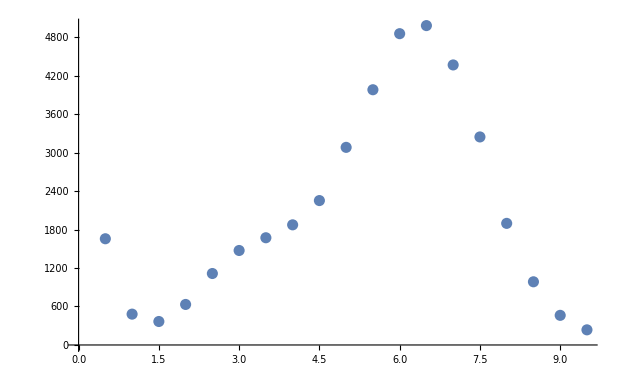

```mathematica
ListPlot[data]
```

```mathematica
data3=({{-6.35, 29143.8}, {-7.95, 29176.5}, {-7.52, 29262.9}, {-7.00, 29330.1}, {-6.67, 29183.5}, {-6.08, 29084.0}, {-5.65, 29298.0}, {-5.26, 29192.2}, {-4.78, 29141.6}, {-4.37, 29166.4}, {-3.73, 29260.7}, {-3.24, 29226.8}, {-2.64, 29228.4}, {-1.88, 29196.6}, {-1.09, 29203.2}, {-0.32, 29096.5}, {4.93, 29526.2}, {6.24, 29589.7}, {5.89, 29510.2}, {5.48, 29599.2}, {5.20, 29523.8}, {4.70, 29405.4}, {4.42, 29320.7}, {4.06, 29127.8}, {3.72, 29009.0}, {3.40, 28819.2}, {2.87, 27559.4}, {2.52, 26662.3}, {2.09, 27344.1}, {1.47, 29095.0}, {0.90, 29360.4}, {0.29, 29334.6}});
```

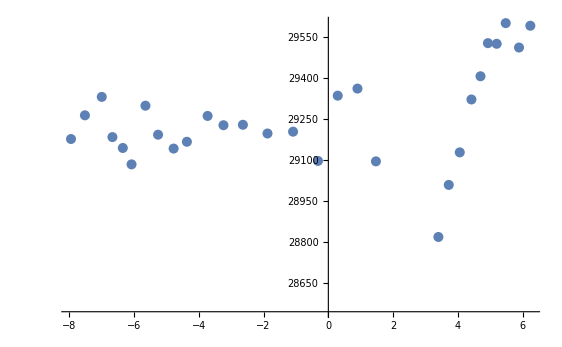

```mathematica
ListPlot[data3]
```

```mathematica
data4=({{-7.86, 12856.8}, {-7.67, 12805.3}, {-7.44, 12786.3}, {-7.14, 12840.4}, {-6.91, 12827.2}, {-6.60, 12827.1}, {-6.42, 12806.0}, {-5.70, 12863.3}, {-5.18, 12815.7}, {-4.79, 12784.7}, {-4.36, 12804.1}, {-3.76, 12848.3}, {-3.24, 12939.2}, {-2.39, 12863.8}, {-1.69, 12850.7}, {-1.30, 12849.7}, {6.19, 13364.8}, {6.06, 12976.8}, {5.84, 12880.0}, {5.64, 12975.1}, {5.36, 12929.2}, {5.14, 12868.1}, {4.96, 12814.3}, {4.39, 12788.4}, {4.00, 12606.6}, {3.75, 12555.0}, {3.38, 12230.3}, {2.91, 11401.7}, {2.53, 10551.5}, {1.86, 11874.8}, {1.34, 12638.6}, {1.07, 12749.1}});
```

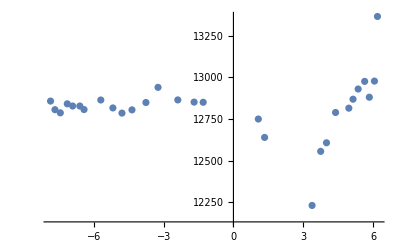

```mathematica
ListPlot[data4]
```

```mathematica
data5=({{-7.79, 3217.4}, {-7.68, 3191.3}, {-7.59, 3176.9}, {-7.39, 3199.3}, {-7.33, 3164.8}, {-7.30, 3164.8}, {-6.91, 3204.7}, {-6.56, 3189.7}, {-6.28, 31169.3}, {-5.65, 3159.4}, {-4.59, 3221.2}, {-3.01, 3160.6}, {-2.91, 3201.6}, {-1.93, 3157.4}, {-1.07, 3176}, {6.09, 3148}, {6.04, 3169.8}, {6, 3202.5}, {5.8, 3205.6}, {5.73, 3173}, {5.71, 3197.8}, {5.37, 3166.8}, {5.08, 3123.1}, {4.91, 3171.2}, {4.38, 3099.9}, {3.57, 2956.2}, {2.36, 2384.9}, {2.32, 2382.9}, {1.57, 2905.4}, {0.89, 3089.9}});
```

```mathematica
data6=({{-7.9, 32618.3}, {-7.64, 32618.3}, {-7.42, 32580.8}, {-7.42, 32500.8}, {-7.19, 32534.4}, {-7.04, 32643.7}, {-6.86, 32480.5}, {-6.61, 32520.7}, {-6.37, 32520.7}, {-5.51, 32431}, {-4.83, 32380}, {-4.30, 32363.9}, {-4.26, 32392.6}, {-3.68, 32088.4}, {-2.97, 31951.2}, {-1.41, 29290.4}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}});
```